```mathematica
SetDirectory[NotebookDirectory[]];
Get["MyPackage.wl"]
```

```mathematica
opts={GridLines->Automatic,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->15},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
Sign[{1,-2}]
```

{1,-1}

```mathematica
SeedRandom[1];
foff=100;
dF={-5,1.2,1.5,2,2.3,2.7,3,4,5,5.2,6,10.8};
Fqupstart=foff+Sign[dF]dF^2
q=Subdivide[1,1.5,Length@Fqupstart-1];
Fqdownstart=(Clip[Fqupstart-foff,{0,Infinity}])^0.8;

Fqup=Interpolation[CombineVec[q,Fqupstart],Method->"Spline"];
Fqdown=Interpolation[CombineVec[q,Fqdownstart],Method->"Spline"];
```

{75,101.44,102.25,104,105.29,107.29,109,116,125,127.04,136,216.64}

```mathematica
arrowcycle[loc_]:= Line[x_]:>{Arrowheads[{0,0,0.05,0}],Arrow[x]}
```

```mathematica
Dynamic@
Block[{qleft=1.1,qright=1.4,thickn=0.006},
Show[
Plot[{Fqdown[qq],Fqup[qq]},{qq,q[[1]],Last@q},GridLines->None,Evaluate@opts,
FrameLabel->{"Generalized displacement (q)","Generated force (F)"},
FrameTicks->Automatic,
PlotRangePadding->Scaled[.15],
Axes->False,
PlotStyle->Directive[Black,Thickness@0.003]],
Plot[Evaluate@{Fqdown[qq],,Fqup[qq],-2000},{qq,qleft,qright},
PlotStyle->{
{Thickness@thickn,Dashed,DefColors[1],Arrowheads[{{-0.05,0.25}}]},
{DefColors[3],Dashed},
{Thickness@thickn,Dashed,DefColors[5],Arrowheads[{{0.05,0.25}}]},
{DefColors[4],Dashed}},
Filling->{1->{3}},
FillingStyle->Directive[DefColors[13],Opacity@0.3],
PlotLegends->AddLegend[{"Initial stretch","Initial stretch","Initial stretch","Initial stretch"}]]/.Line->Arrow,
Graphics[{Thickness@thickn,Dashed,
DefColors[3],Line[{{qleft,Fqdown[qleft]},{qleft,Fqup[qleft]}}]/.Line[x_]:>{Arrowheads[{0,0,0.05,0}],Arrow[x]},
DefColors[4],Line[{{qright,Fqdown[qright]},{qright,Fqup[qright]}}]/.Line[x_]:>{Arrowheads[{0,-0.05,0,0}],Arrow[x]}
}]
]]
```

```mathematica
DefColors[;;]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
ColorData["Crayola"]["MangoTango"]
```

```mathematica
Dynamic@ListPlot[CombineVec[Range[1,Length@Fqup],Fqup],Joined->True,PlotRange->{Automatic,Automatic}]
```

```mathematica
FinishDynamic@Fq
```

FinishDynamic[]

```mathematica
Fq//Head
```

Dynamic

```mathematica
Dynamic[{list={},EventHandler[Dynamic[Framed@Graphics[{Red,Line[list],Point[list]},PlotRange->2]],{"MouseClicked":>AppendTo[list,MousePosition["Graphics"]]}],Fq=Dynamic@list[[;;,2]]}]
```

```mathematica
tmp=Fq//Flatten
```

```mathematica
tmp[[]]
```

Dynamic

```mathematica
Fq//Head
```

Dynamic

```mathematica
Fq[[1]]
```

{}

```mathematica
Fqup={};
Block[{i,k},Do[{
If[Fq[[i]]<Fq[[i+1]],AppendTo[Fqup,Fq[[i]]];,{AppendTo[Fqup,Fq[[i]]];Break[]}]}
,{i,1,Length@Fq-1}]]
Fqup
```

{}

```mathematica
FindInstance[Fqup==list,Booleans]
```

{}

```mathematica
Fqdown=list[[Position[list,Last@Fqup][[1,1]]+1;;Length@list]]
```

{{-1.46216,-0.366707},{-1.17883,-0.320873},{-0.916328,-0.26254},{-0.724662,-0.170873},{-0.424662,-0.0250399},{0.0586717,0.141627},{0.262838,0.158293},{0.442005,0.26246},{0.592005,0.379127},{0.708672,0.466627},{0.875338,0.59996},{0.946172,0.658293}}

```mathematica
Fqdown=
```

```mathematica
Clear@k
```

```mathematica
list[[1]]
```

{-1.44966,0.82496}

```mathematica
Fqup=list
```

{{-1.44966,0.82496},{-1.20799,0.94996},{-0.932995,0.98746},{-0.720495,1.02496},{-0.537162,1.07913},{-0.228828,1.17079},{0.0170051,1.25413},{0.275338,1.37913},{0.583672,1.49163},{0.792005,1.56246},{0.900338,1.63329},{-1.46216,-0.366707},{-1.17883,-0.320873},{-0.916328,-0.26254},{-0.724662,-0.170873},{-0.424662,-0.0250399},{0.0586717,0.141627},{0.262838,0.158293},{0.442005,0.26246},{0.592005,0.379127},{0.708672,0.466627},{0.875338,0.59996},{0.946172,0.658293}}

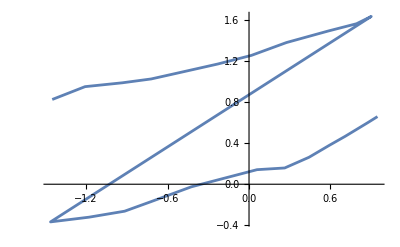

```mathematica
ListPlot[list,Joined->True]
```